```mathematica
ClearAll["Global`*"]
<<MaTeX`
```

## System parameter analysis

### Constants

```mathematica
e = Quantity[(1.602176)*10^(-19),"Coulombs"];  (*electron's charge*)
hbar = Quantity[(1.054571)*10^(-34),("Kilograms"*"Meters"^2)/"Seconds"]; (*Plank's constant*)
m= Quantity[(9.109383)*10^(-31),"Kilograms"]; (*electron's mass*)
c = Quantity[(2.997924)*10^(8),"Meters"/"Seconds"]; (*speed of light in vacuum*)
ϵ0 = Quantity[(8.854187)*10^(-12),("Coulombs"^2*"Seconds"^2)/("Kilograms"*"Meters"^(3))]; (*vacuum permittivity*)
eV = Quantity[(1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))](*electron Volts*)
```

1.60218×10^-19 kg m^2/s^2

### System parameters

```mathematica
B = Quantity[(1.2),"Kilograms"/("Coulombs"*"Seconds")]; (*Stationary magnetic field's amplitude = 1.2 T*)
ElecInt0= Quantity[(1)*10^(6),"Kilograms"/"Seconds"^(3)]; (*Reference dressing electric field's intensity = 100 Wcm^-2*)
ω = Quantity[(2)*10^(12),"Seconds"^(-1)]; (*Dressing field's frequency = 2×10^12 rads^-1*)
me = 0.071*m;  (*Effective electron's mass for 2DEG = 0.071m*)
```

### Parameter calculation

```mathematica
ω0 = (e*B)/(me);(*cyclotron frequency*) 
E0 = Sqrt[(2*ElecInt0)/(c*ϵ0 )](*Reference dressing electric field's amplitude*)
b= (e*E0*((ω0 )^2))/(hbar*ω*((ω0 )^2-(ω)^2));(*Pre-defined parameter*)
κ = Sqrt[me*ω0 /hbar]; (*Pre-defined parameter in Gauss-Hermite functions*)
Subscript[λ, 1] = (hbar* b)/(e*B);(*Pre-defined parameter in inverse scattering time*)
Subscript[λ, 2] = (hbar *κ )/(e*B); (*Pre-defined parameter in inverse scattering time*)
ϵN = hbar*ω0 *1000/eV;
```

27449.2 kg m/(s^2 C)

### Parameter values

```mathematica
k0 =Quantity[1*10^(8),"Meters"^(-1)];
```

```mathematica
λ1 = NumberForm[Subscript[λ, 1]*k0,4]
```

2.09

```mathematica
λ2 = NumberForm[Subscript[λ, 2]*k0,4]
```

2.342

## Landau level wavefunction χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

We can define normalized dressed electric field intensity = ElecInt := (Real electric field intensity)/ElecInt0 where ElecInt0 =  100 Wcm^-2.

### Landau level N=0

```mathematica
Q0:= χ[2.342*k2,0]*χ[2.342*(k1-k2),0];
A0[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q0,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup0 := NIntegrate[A0[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown0:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse0 := Sup0/Sdown0;
```

### Landau level N=1

```mathematica
Q1:= χ[2.342*k2,1]*χ[2.342*(k1-k2),1];
A1[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q1,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup1:= NIntegrate[A1[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown1:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse1 := Sup1/Sdown1;
```

### Landau level N=2

```mathematica
Q2:= χ[2.342*k2,2]*χ[2.342*(k1-k2),2];
A2[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q2,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup2:= NIntegrate[A2[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown2:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse2 := Sup2/Sdown2;
```

### Landau level N=3

```mathematica
Q3:= χ[2.342*k2,3]*χ[2.342*(k1-k2),3];
A3[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q3,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup3:= NIntegrate[A3[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown3:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse3:= Sup3/Sdown3;
```

### Landau level N=4

```mathematica
Q4:= χ[2.342*k2,4]*χ[2.342*(k1-k2),4];
A4[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q4,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup4:= NIntegrate[A4[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown4:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse4:= Sup4/Sdown4;
```

## Inverse scattering time matrix central element analysis (l=0)

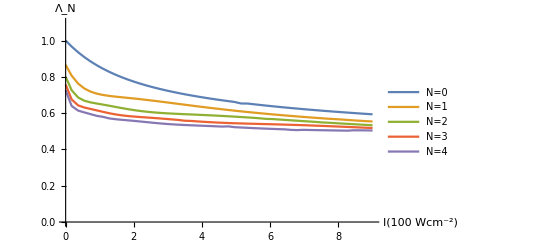

```mathematica
P=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{e,0,9},
PlotRange->{{0,9},{0,1.1}},
PlotLegends->{"N=0","N=1","N=2","N=3","N=4"},AxesLabel->{Style["I(100 Wcm^-2)",FontFamily->"Times New Roman",FontSize->14.5],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50]
```

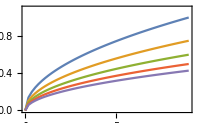

```mathematica
P1=Plot[{Sqrt[e]/3,Sqrt[e]/4,Sqrt[e]/5,Sqrt[e]/6,Sqrt[e]/7} ,{e,0,9},
PlotRange->{{0,9},{0,1.1}},
PlotLegends->{MaTeX["N=1"],MaTeX["N=2"],MaTeX["N=3"],MaTeX["N=4"],MaTeX["N=5"]},
MaxRecursion->0,
PlotPoints->50,
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\Lambda_{N}"],None},{MaTeX["I(100~\\text{W}\\text{cm}^{-2})"],None}},
ImageSize->200]
```

```mathematica
Export["nnn.pdf",P1]
```

nnn.pdf